```mathematica
eps28tot[x_]:=eps28Re[x]+I eps28Im[x]
eps28totData=Table[{x,eps28tot[x]},{x,1.19,4.83,0.01}];
```

```mathematica
eps28DataIm=Table[{x,eps28Im[x]},{x,xmin,xmax,0.01}];
eps28DataRe=Table[{x,eps28Re[x]},{x,xmin,xmax,0.01}];
```

```mathematica
eps28DataTot=Table[eps28Re[x]+ I eps28Im[x],{x,xmin,xmax,0.01}];
omega28=Range[xmin,xmax,0.01];
n=Length[omega28];
```

```mathematica
epsModel[ω_, A1_, ω01_, γ1_,  A2_, ω02_, γ2_,  A3_, ω03_, γ3_,  A4_, ω04_, γ4_,  A5_, ω05_, γ5_,  A6_, ω06_, γ6_] :=
 1 +  A1/(ω01^2 - ω^2 - I γ1 ω) +  A2/(ω02^2 - ω^2 - I γ2 ω) +  A3/(ω03^2 - ω^2 - I γ3 ω) +  A4/(ω04^2 - ω^2 - I γ4 ω) +  A5/(ω05^2 - ω^2 - I γ5 ω) +  A6/(ω06^2 - ω^2 - I γ6 ω);
epsModel10[ω_, A1_, ω01_, γ1_,  A2_, ω02_, γ2_,  A3_, ω03_, γ3_,  A4_, ω04_, γ4_,  A5_, ω05_, γ5_, A6_,ω06_,γ6_,A7_, ω07_, γ7_,A8_, ω08_, γ8_,A9_, ω09_,γ9_,A10_,ω010_,γ10_] :=
 1 +  A1/(ω01^2 - ω^2 - I γ1 ω) +  A2/(ω02^2 - ω^2 - I γ2 ω) +  A3/(ω03^2 - ω^2 - I γ3 ω) +  A4/(ω04^2 - ω^2 - I γ4 ω) +  A5/(ω05^2 - ω^2 - I γ5 ω) +  A6/(ω06^2 - ω^2 - I γ6 ω)+  A7/(ω07^2 - ω^2 - I γ7 ω)+  A8/(ω08^2 - ω^2 - I γ8 ω)+  A9/(ω09^2 - ω^2 - I γ9 ω)+  A10/(ω010^2 - ω^2 - I γ10 ω);
```

```mathematica
errorFunction[A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_,A5_,ω05_,γ5_,A6_,ω06_,γ6_]:=Sum[Abs[epsModel[omega28[[i]],A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6]-eps28DataTot[[i]]]^2,{i,1,n}]

errorFunction10[A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_,A5_,ω05_,γ5_,A6_,ω06_,γ6_,A7_, ω07_, γ7_,A8_, ω08_, γ8_,A9_, ω09_,γ9_,A10_,ω010_,γ10_]:=Sum[Abs[epsModel10[omega28[[i]],A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6,A7,ω07,γ7,A8,ω08,γ8,A9,ω09,γ9,A10,ω010,γ1]-eps28DataTot[[i]]]^2,{i,1,n}]
```

```mathematica
fit=NMinimize[{errorFunction[A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6],(*restricciones físicas*)A1>0&&A2>0&&A3>0&&A4>0&&A5>0&&A6>0&&γ1>0&&γ2>0&&γ3>0&&γ4>0&&γ5>0&&γ6>0&&ω01>0&&ω02>0&&ω03>0&&ω04>0&&ω05>0&&ω06>0&&ω01<ω02<ω03<ω04<ω05<ω06},{A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6},Method->"NelderMead",MaxIterations->10000]
```

{0.0623576,{A1→0.,ω01→1.68175,γ1→145.716,A2→0.,ω02→1.68328,γ2→64.6879,A3→16.9152,ω03→15.2936,γ3→1.27946,A4→207.726,ω04→15.2936,γ4→0.247027,A5→1.26022,ω05→44.0503,γ5→0.00217777,A6→3.89967,ω06→44.0539,γ6→36.7094}}

```mathematica
fit61=NMinimize[{errorFunction[A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6],(*restricciones físicas*)A1>0&&A2>0&&A3>0&&A4>0&&A5>0&&A6>0&&γ1>0&&γ2>0&&γ3>0&&γ4>0&&γ5>0&&γ6>0&&ω01>0&&ω02>0&&ω03>0&&ω04>0&&ω05>0&&ω06>0},{A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6},Method->"NelderMead",MaxIterations->5000]
```

{0.0123374,{A1→13.7715,ω01→135.473,γ1→44.3999,A2→0.548472,ω02→80.785,γ2→37.9828,A3→10.3358,ω03→73.9636,γ3→86.1981,A4→7.46361,ω04→102.781,γ4→188.398,A5→200.826,ω05→14.5094,γ5→0.112283,A6→0.0245821,ω06→2.99779,γ6→0.178069}}

```mathematica
fit101=NMinimize[{errorFunction10[A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6,A7,ω07,γ7,A8,ω08,γ8,A9,ω09,γ9,A10,ω010,γ10],A1>0&&A2>0&&A3>0&&A4>0&&A5>0&&A6>0&&A7>0&&A8>0&&A9>0&&A10>0&&γ1>0&&γ2>0&&γ3>0&&γ4>0&&γ5>0&&γ6>0&&γ7>0&&γ8>0&&γ9>0&&γ10>0&&ω01>0&&ω02>0&&ω03>0&&ω04>0&&ω05>0&&ω06>0&&ω07>0&&ω08>0&&ω09>0&&ω010>0},{A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6,A7,ω07,γ7,A8,ω08,γ8,A9,ω09,γ9,A10,ω010,γ10},Method->"NelderMead",MaxIterations->10000]
```

```mathematica
paramRules=fit[[2]];
epsFit[ω_]:=epsModel[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6]/. paramRules
paramRules2=fit61[[2]];
epsFit2[ω_]:=epsModel[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6]/. paramRules2
```

```mathematica
paramRules10=fit101[[2]];
epsFit10[ω_]:=epsModel10[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6,A7,ω07,γ7,A8,ω08,γ8,A9,ω09,γ9,A10,ω010,γ10]/. paramRules10
```

```mathematica
epsFit10[3]
```

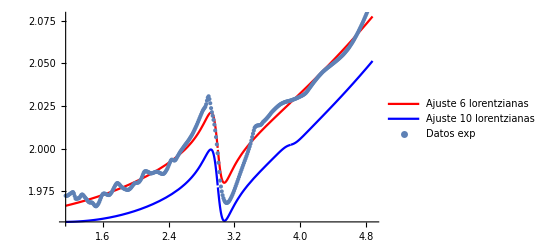

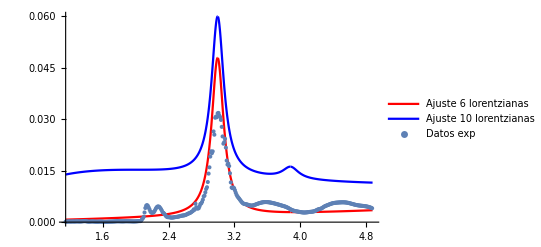

```mathematica
Show[Plot[{Re[epsFit2[w]],Re[epsFit10[w]]},{w,xmin,xmax},PlotLegends->{"Ajuste 6 lorentzianas","Ajuste 10 lorentzianas"},PlotStyle->{Red,Blue}],ListPlot[{eps28DataRe},PlotLegends->{"Datos exp"},PlotRange->All]]
Show[Plot[{Im[epsFit2[w]],Im[epsFit10[w]]},{w,xmin,xmax},PlotLegends->{"Ajuste 6 lorentzianas","Ajuste 10 lorentzianas"},PlotStyle->{Red,Blue},PlotRange->All],ListPlot[{eps28DataIm},PlotLegends->{"Datos exp"}],PlotRange->All]
```

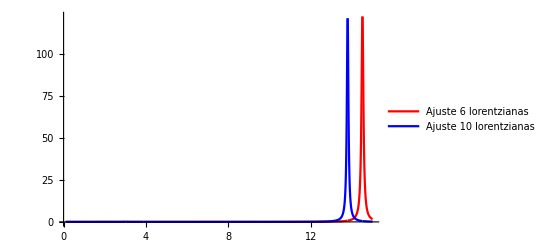

```mathematica
Plot[{Im[epsFit2[w]],Im[epsFit10[w]]},{w,0.1,15},PlotLegends->{"Ajuste 6 lorentzianas","Ajuste 10 lorentzianas"},PlotStyle->{Red,Blue},PlotRange->All]
```

```mathematica
lorentzSumIm16[w,13.771451477955294,135.47335844521166,44.3998917445662,0.5484718748840071,80.78502398714583,37.982821584085876,10.335832563497105,73.96355998278301,86.19805550349906,]
```

```mathematica
lorentzSumIm10[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_,A5_,ω05_,γ5_,A6_,ω06_,γ6_,A7_,ω07_,γ7_,A8_,ω08_,γ8_,A9_,ω09_,γ9_,A10_,ω010_,γ10_]:=A1 lorentzIm[ω,ω01,γ1]+A2 lorentzIm[ω,ω02,γ2]+A3 lorentzIm[ω,ω03,γ3]+ A4 lorentzIm[ω,ω04,γ4]+ A5 lorentzIm[ω,ω05,γ5]+A6 lorentzIm[ω,ω06,γ6]+A7 lorentzIm[ω,ω07,γ7]+A8 lorentzIm[ω,ω08,γ8]+A9 lorentzIm[ω,ω09,γ9]+A10 lorentzIm[ω,ω010,γ10];
(*Definición de 4 lorentzianas*)
lorentzSumRe10[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_,A5_,ω05_,γ5_,A6_,ω06_,γ6_,A7_,ω07_,γ7_,A8_,ω08_,γ8_,A9_,ω09_,γ9_,A10_,ω010_,γ10_]:= lorentzRe[A1,ω,ω01,γ1]+lorentzRe[A2,ω,ω02,γ2]+ lorentzRe[A3,ω,ω03,γ3]+lorentzRe[A4,ω,ω04,γ4]+lorentzRe[A5,ω,ω05,γ5]+lorentzRe[A6,ω,ω06,γ6]+lorentzRe[A7,ω,ω07,γ7]+lorentzRe[A8,ω,ω08,γ8]+lorentzRe[A9,ω,ω09,γ9]+lorentzRe[A10,ω,ω010,γ10]-9;
```

```mathematica
lorentzSum[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_,A5_,ω05_,γ5_,A6_,ω06_,γ6_]:=lorentz[A1,ω,ω01,γ1]+lorentz[A2,ω,ω02,γ2]+ lorentz[A3,ω,ω03,γ3]+lorentz[A4,ω,ω04,γ4]+lorentz[A5,ω,ω05,γ5]+lorentz[A6,ω,ω06,γ6]-5;
```

```mathematica
lorentzSumIm10[5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5]
```

2

```mathematica
complex28=NonlinearModelFit[eps28DataTot,{lorentzSum[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6],A1>0&&A2>0&&A3>0&&A4>0&&A5>0&&A6>0&&γ1>0&&γ2>0&&γ3>0&&γ4>0&&γ5>0&&γ6>0&&ω06>ω05>ω04>ω03>ω02>ω01>0},{{A1,fit15Values[[1]]},{ω01,fit28Values[[2]]},{γ1,fit15Values[[3]]},{A2,fit15Values[[4]]},{ω02,fit15Values[[5]]},{γ2,fit15Values[[6]]},{A3,fit15Values[[7]]},{ω03,fit15Values[[8]]},{γ3,fit28Values[[9]]},{A4,fit15Values[[10]]},{ω04,fit15Values[[11]]},{γ4,fit15Values[[12]]},{A5,fit15Values[[13]]},{ω05,fit28Values[[14]]},{γ5,fit28Values[[15]]},{A6,fit281Values[[1]]},{ω06,fit281Values[[2]]},{γ6,fit281Values[[3]]}},ω]
```

NonlinearModelFit::nrnum: The function value 2980.43-7.06236 ⅈ is not a real number at {A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,«8»} = {0.000383677,2.13957,0.0539125,0.000699595,2.29116,0.1008,0.0151683,3.00063,0.212506,0.00605578,«8»}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,«8»} = {0.000383677,2.13957,0.0539125,0.000699595,2.29116,0.1008,0.0151683,3.00063,0.212506,0.00605578,«8»}.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,«8»} = {0.001,2.13957,0.0539125,0.001,2.29116,0.1008,0.0151683,3.00063,0.212506,0.00605578,«8»}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[«1»] failed at {0.001,2.13957,0.0539125,0.001,2.29116,0.1008,0.0151683,3.00063,0.212506,0.00605578,«8»}.

NonlinearModelFit::nrnum: The function value 2980.43-7.06236 ⅈ is not a real number at {A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,«8»} = {0.000383677,2.13957,0.0539125,0.000699595,2.29116,0.1008,0.0151683,3.00063,0.212506,0.00605578,«8»}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,«8»} = {0.000383677,2.13957,0.0539125,0.000699595,2.29116,0.1008,0.0151683,3.00063,0.212506,0.00605578,«8»}.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[«1»] failed at {0.001,2.13957,0.0539125,0.001,2.29116,0.1008,0.0151683,3.00063,0.212506,0.00605578,«8»}.

```mathematica
fit28complex=ResourceFunction["MultiNonlinearModelFit"][{eps28DataRe,eps28DataIm},{lorentzSumRe6[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6],lorentzSumIm6[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6],A1>0,A2>0,A3>0,A4>0,A5>0,A6>0,γ1>0,γ2>0,γ3>0,γ4>0,γ5>0,γ6>0,ω01>0,ω02>0,ω03>0,ω04>0,ω05>0,ω06>0,ω01<ω02<ω03<ω04<ω05<ω06},{{A1,fit15Values[[1]]},{ω01,fit15Values[[2]]},{γ1,fit15Values[[3]]},{A2,fit15Values[[4]]},{ω02,fit15Values[[5]]},{γ2,fit15Values[[6]]},{A3,fit15Values[[7]]},{ω03,fit15Values[[8]]},{γ3,fit15Values[[9]]},{A4,fit15Values[[10]]},{ω04,fit15Values[[11]]},{γ4,fit15Values[[12]]},{A5,fit15Values[[13]]},{ω05,fit15Values[[14]]},{γ5,fit15Values[[15]]},{A6,fit151Values[[1]]},{ω06,fit151Values[[2]]},{γ6,fit151Values[[3]]}},{ω},MaxIterations->10000];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 10000 iterations.

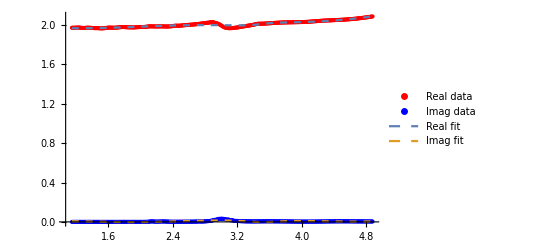

```mathematica
Show[ListPlot[{eps28DataRe,eps28DataIm},PlotStyle->{Red,Blue},PlotLegends->{"Real data","Imag data"}],Plot[{fit28complex[1,ω],fit28complex[2,ω]},{ω,Min[eps28DataRe[[All,1]]],Max[eps28DataIm[[All,1]]]},PlotStyle->{Dashed,Dashed},PlotLegends->{"Real fit","Imag fit"}]]
```

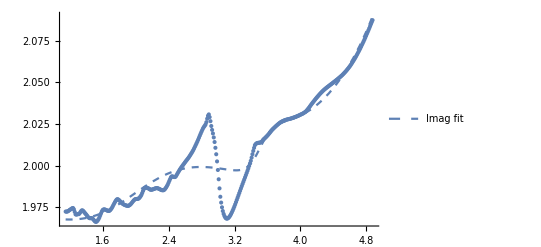

```mathematica
Show[ListPlot[{eps28DataRe},PlotLegends->{"Re data"}],Plot[{fit28complex[1,ω]},{ω,Min[eps28DataRe[[All,1]]],Max[eps28DataIm[[All,1]]]},PlotStyle->{Dashed,Dashed},PlotLegends->{"Re fit"}],PlotRange->All]
```

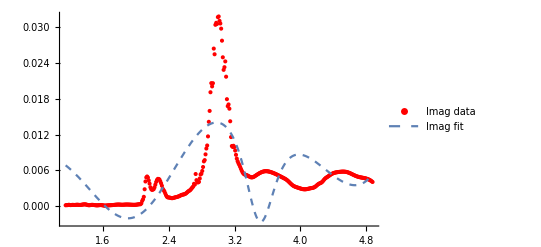

```mathematica
Show[ListPlot[{eps28DataIm},PlotStyle->{Red,Blue},PlotLegends->{"Imag data"}],Plot[{fit28complex[2,ω]},{ω,Min[eps28DataRe[[All,1]]],Max[eps28DataIm[[All,1]]]},PlotStyle->{Dashed,Dashed},PlotLegends->{"Imag fit"}],PlotRange->All]
```

```mathematica
fit28complex2=ResourceFunction["MultiNonlinearModelFit"][{eps28DataRe,eps28DataIm},{lorentzSumRe10[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6,A7,ω07,γ7,A8,ω08,γ8,A9,ω09,γ9,A10,ω010,γ10],lorentzSumIm10[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6,A7,ω07,γ7,A8,ω08,γ8,A9,ω09,γ9,A10,ω010,γ10],A1>0,A2>0,A3>0,A4>0,A5>0,A6>0,A7>0,A8>0,A9>0,A10>0,γ1>0,γ2>0,γ3>0,γ4>0,γ5>0,γ6>0,ω01>0,ω02>0,ω03>0,ω04>0,ω05>0,ω06>0,ω07>0,ω08>0,ω09>0,ω010>0,ω01<ω02<ω03<ω04<ω05<ω06<ω07<ω08<ω09<ω010},{{A1,fit15Values[[1]]},{ω01,fit15Values[[2]]},{γ1,fit15Values[[3]]},{A2,fit15Values[[4]]},{ω02,fit15Values[[5]]},{γ2,fit15Values[[6]]},{A3,fit15Values[[7]]},{ω03,fit15Values[[8]]},{γ3,fit15Values[[9]]},{A4,fit15Values[[10]]},{ω04,fit15Values[[11]]},{γ4,fit15Values[[12]]},{A5,fit15Values[[13]]},{ω05,fit15Values[[14]]},{γ5,fit15Values[[15]]},{A6,fit151Values[[1]]},{ω06,fit151Values[[2]]},{γ6,fit151Values[[3]]},{A7,fit15Values[[1]]},{ω07,fit15Values[[2]]},{γ7,fit15Values[[3]]},{A8,fit15Values[[4]]},{ω08,fit15Values[[5]]},{γ8,fit15Values[[6]]},{A9,fit15Values[[7]]},{ω09,fit15Values[[8]]},{γ9,fit15Values[[9]]},{A10,fit15Values[[10]]},{ω010,fit15Values[[11]]},{γ10,fit15Values[[12]]}},{ω},MaxIterations->20000];
```

$Aborted